```mathematica
SetDirectory[NotebookDirectory[]]
ClearAll["Global`*"]
```

C:\Users\Boris\Documents\These\PyFFTDMA\Mickael\Python\FinalCampainResults

```mathematica
Matrix60=Import["ParametersMatrix60.xml"];
Matrix8=Import["ParametersMatrix8.xml"];
Matrix2=Import["ParametersMatrix2.xml"];
```

```mathematica
α0
```

```mathematica
α0Data={Matrix2[[2]],Matrix8[[2]],Matrix60[[2]]};
α0Data//MatrixForm
α0Data5 = Transpose[α0Data][[1]];
α0Data15 = Transpose[α0Data][[2]];
α0Data25 = Transpose[α0Data][[3]];
NList={2,8,60};
TauxList = {5,15,25};
```

(3812.44 | 5130.44 | 6717.73
3999.46 | 6127.89 | 9748.06
4152.8 | 6579.47 | 10140.4)

```mathematica
α0Plot5 = Transpose@{NList,α0Data5};
α0Plot15 = Transpose@{NList,α0Data15};
α0Plot25 = Transpose@{NList,α0Data25};
α05Fit= NonlinearModelFit[α0Plot5,Last[α0Plot5][[2]]( 1-Exp[-B x+CC]),{B,CC},x,MaxIterations->1000];
α015Fit= NonlinearModelFit[α0Plot15,Last[α0Plot15][[2]](1-Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
α025Fit= NonlinearModelFit[α0Plot25,Last[α0Plot25][[2]](1-Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
P1=ListPlot[{α0Plot5,α0Plot15,α0Plot25},PlotMarkers->{Automatic,15},PlotStyle->Black,AxesStyle->Directive[ Black, 24,FontFamily-> "Times New Roman"],ImageSize->{600},PlotLegends->{Style["Data points 5%",FontFamily->"Times New roman",24],Style["Data points 15%",FontFamily->"Times New roman",24],Style["Data points 25%",FontFamily-> "Times New Roman",24]},AxesLabel->{Style["N Value",FontFamily->"Times New Roman"],Style["Moduli (MPa)",FontFamily->"Times New roman"]}];
P2 = Plot[{α05Fit[x],α015Fit[x],α025Fit[x]},{x,2,60},PlotLegends->{Style["5%",FontFamily->"Times New roman",24],Style["15%",FontFamily->"Times New roman",24],Style["25%",FontFamily-> "Times New Roman",24]},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 24]];
```

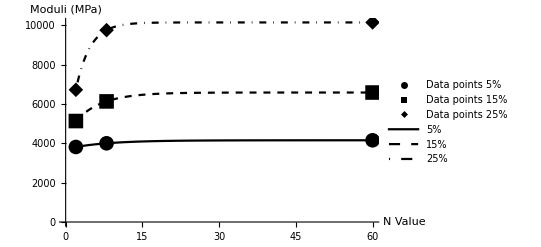

```mathematica
PlotExport =Show[P1,P2]
```

```mathematica
Export["Alpha0plot.eps",PlotExport]
```

Alpha0plot.eps

FittedModel[0.141664-0.00438451 x+0.000526316 x^2]

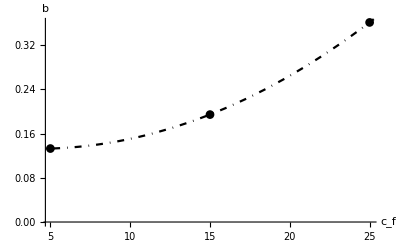

Alpha0B.eps

```mathematica
Bα0={B/.α05Fit[[1]][[2]],B/.α015Fit[[1]][[2]],B/.α025Fit[[1]][[2]]};
Ba0Plot = Transpose@{TauxList,Bα0};
Bα0Fit= NonlinearModelFit[Ba0Plot,A x^2+B x+CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{Ba0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{250},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["b",FontFamily->"Times New Roman",18]}];
P2 = Plot[{Bα0Fit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Alpha0B.eps",PlotExport]
```

FittedModel[3364.82+129.238 x+5.67145 x^2]

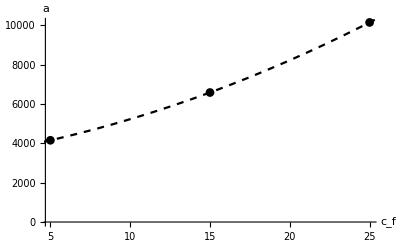

Alpha0A.eps

```mathematica
Aα0={Last[α0Plot5][[2]],Last[α0Plot15][[2]],Last[α0Plot25][[2]]};
Aa0Plot = Transpose@{TauxList,Aα0};
Aα0Fit= NonlinearModelFit[Aa0Plot,A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{Aa0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{250},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["a",FontFamily->"Times New Roman",18]}];
P2 = Plot[{Aα0Fit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Alpha0A.eps",PlotExport]
```

FittedModel[-2.92299+0.146227 x-0.00175488 x^2]

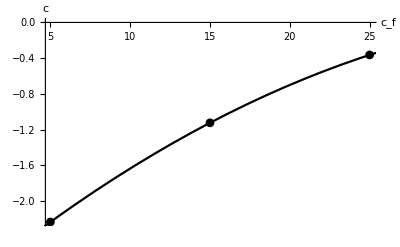

Alpha0C.eps

```mathematica
CCα0={CC/.α05Fit[[1]][[2]],CC/.α015Fit[[1]][[2]],CC/.α025Fit[[1]][[2]]};
CCa0Plot = Transpose@{TauxList,CCα0};
CCα0Fit= NonlinearModelFit[CCa0Plot,A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCa0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{250},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["c",FontFamily->"Times New Roman",18]}];
P2 = Plot[{CCα0Fit[x]},{x,2,60},PlotStyle->{Black},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Alpha0C.eps",PlotExport]
```

```mathematica
Metaα0Value[Taux_,NVal_]:=Aα0Fit[Taux](1- Exp[-Bα0Fit[Taux] NVal+CCα0Fit[Taux]])
```

```mathematica
Metaα0Value[20,6]
```

7383.77

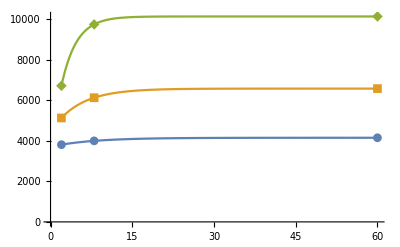

```mathematica
P1=ListPlot[{α0Plot5,α0Plot15,α0Plot25},PlotMarkers->Automatic];
P2 = Plot[{Metaα0Value[5,x],Metaα0Value[15,x],Metaα0Value[25,x]},{x,2,60}];
Show[P1,P2]
```

```mathematica
β0
```

```mathematica
β0Data={Matrix2[[3]],Matrix8[[3]],Matrix60[[3]]};
β0Data//MatrixForm
β0Data5 = Transpose[β0Data][[1]];
β0Data15 = Transpose[β0Data][[2]];
β0Data25 = Transpose[β0Data][[3]];
NList={2,8,60};
TauxList = {5,15,25};
```

(7033.98 | 8095.05 | 9600.58
6922.76 | 7726.24 | 8691.4
6863.88 | 7576.37 | 8507.32)

```mathematica
β0Plot5 = Transpose@{NList,β0Data5};
β0Plot15 = Transpose@{NList,β0Data15};
β0Plot25 = Transpose@{NList,β0Data25};
β05Fit= NonlinearModelFit[β0Plot5,Last[β0Plot5][[2]](1+ Exp[-B x+CC]),{B,CC},x,MaxIterations->1000];
β015Fit= NonlinearModelFit[β0Plot15,Last[β0Plot15][[2]](1+ Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
β025Fit= NonlinearModelFit[β0Plot25,Last[β0Plot25][[2]](1+Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
P1=ListPlot[{β0Plot5,β0Plot15,β0Plot25},PlotMarkers->{Automatic,15},PlotStyle->Black,AxesStyle->Directive[ Black, 24,FontFamily-> "Times New Roman"],ImageSize->{600},PlotLegends->{Style["Data points 5%",FontFamily->"Times New roman",18],Style["Data points 15%",FontFamily->"Times New roman",18],Style["Data points 25%",FontFamily-> "Times New Roman",18]},AxesLabel->{Style["N Value",FontFamily->"Times New Roman"],Style["Moduli (MPa)",FontFamily->"Times New roman"]}];
P2 = Plot[{β05Fit[x],β015Fit[x],β025Fit[x]},{x,2,60},PlotLegends->{Style["5%",FontFamily->"Times New roman",18],Style["15%",FontFamily->"Times New roman",18],Style["25%",FontFamily-> "Times New Roman",18]},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 24]];
```

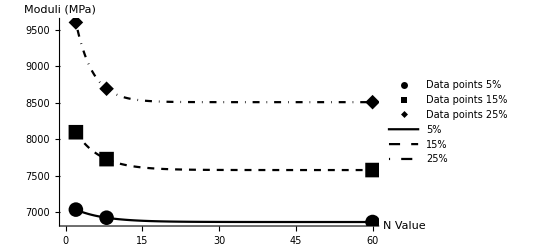

```mathematica
PlotExport=Show[P1,P2]
```

```mathematica
Export["Beta0plot.eps",PlotExport]
```

Beta0plot.eps

FittedModel[0.184217-0.00297869 x+0.000299484 x^2]

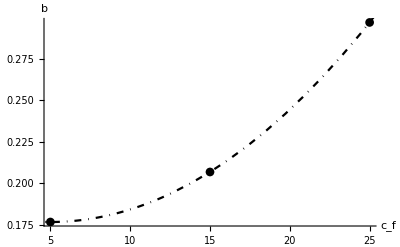

Beta0B.eps

FittedModel[6589.54+49.4054 x+1.09223 x^2]

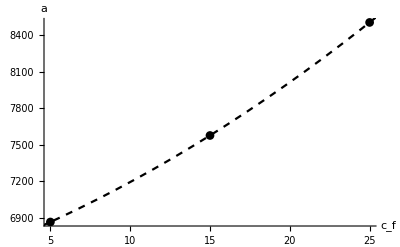

Beta0A.eps

FittedModel[-3.98211+0.134288 x-0.00133279 x^2]

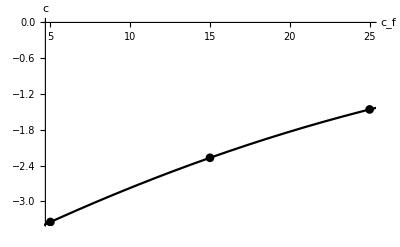

Beta0C.eps

```mathematica
Bβ0={B/.β05Fit[[1]][[2]],B/.β015Fit[[1]][[2]],B/.β025Fit[[1]][[2]]};
Bβ0Plot = Transpose@{TauxList,Bβ0};
Bβ0Fit= NonlinearModelFit[Bβ0Plot,A x^2+B x+CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{Bβ0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["b",FontFamily->"Times New Roman",18]}];
P2 = Plot[{Bβ0Fit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Beta0B.eps",PlotExport]

Aβ0={Last[β0Plot5][[2]],Last[β0Plot15][[2]],Last[β0Plot25][[2]]};
Aβ0Plot = Transpose@{TauxList,Aβ0};
Aβ0Fit= NonlinearModelFit[Aβ0Plot,A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{Aβ0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["a",FontFamily->"Times New Roman",18]}];
P2 = Plot[{Aβ0Fit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Beta0A.eps",PlotExport]

CCβ0={CC/.β05Fit[[1]][[2]],CC/.β015Fit[[1]][[2]],CC/.β025Fit[[1]][[2]]};
CCβ0Plot = Transpose@{TauxList,CCβ0};
CCβ0Fit= NonlinearModelFit[CCβ0Plot,A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCβ0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["c",FontFamily->"Times New Roman",18]}];
P2 = Plot[{CCβ0Fit[x]},{x,2,60},PlotStyle->{Black},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Beta0C.eps",PlotExport]
```

```mathematica
Aβ0={Last[β0Plot5][[2]],Last[β0Plot15][[2]],Last[β0Plot25][[2]]};
Aa0Plot = Transpose@{TauxList,Aβ0};
Aβ0Fit= NonlinearModelFit[Aa0Plot,A x+B,{A,B},x,MaxIterations->500]
```

FittedModel[6416.61+82.1722 x]

FittedModel[-3.77108+0.0943039 x]

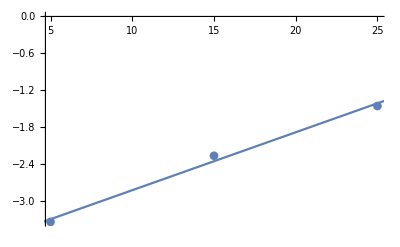

```mathematica
CCβ0={CC/.β05Fit[[1]][[2]],CC/.β015Fit[[1]][[2]],CC/.β025Fit[[1]][[2]]};
CCa0Plot = Transpose@{TauxList,CCβ0};
CCβ0Fit= NonlinearModelFit[CCa0Plot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCa0Plot},PlotMarkers->Automatic];
P2 = Plot[{CCβ0Fit[x]},{x,2,60}];
Show[P1,P2]
```

```mathematica
Metaβ0Value[Taux_,NVal_]:=Aβ0Fit[Taux](1+ Exp[-Bβ0Fit[Taux] NVal+CCβ0Fit[Taux]])
```

```mathematica
Metaβ0Value[15,4]
```

7965.95

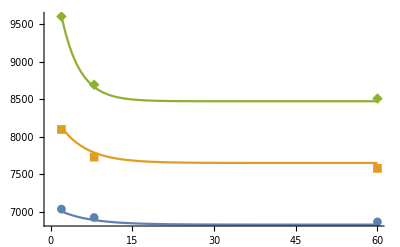

```mathematica
P1=ListPlot[{β0Plot5,β0Plot15,β0Plot25},PlotMarkers->Automatic];
P2 = Plot[{Metaβ0Value[5,x],Metaβ0Value[15,x],Metaβ0Value[25,x]},{x,2,60}];
Show[P1,P2]
```

λ0

(4793.21 | 5601.5 | 6481.32
4809.82 | 5651.32 | 6479.39
4807.69 | 5579.48 | 6345.75)

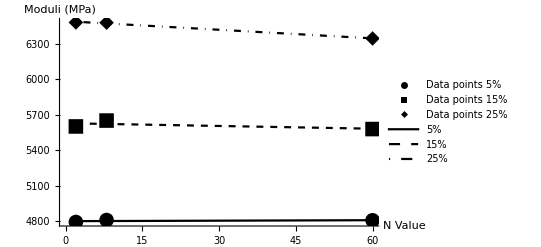

```mathematica
λ0
λ0Data={Matrix2[[4]],Matrix8[[4]],Matrix60[[4]]};
λ0Data//MatrixForm
λ0Data5 = Transpose[λ0Data][[1]];
λ0Data15 = Transpose[λ0Data][[2]];
λ0Data25 = Transpose[λ0Data][[3]];
NList={2,8,60};
TauxList = {5,15,25};

λ0Plot5 = Transpose@{NList,λ0Data5};
λ0Plot15 = Transpose@{NList,λ0Data15};
λ0Plot25 = Transpose@{NList,λ0Data25};
λ05Fit= NonlinearModelFit[λ0Plot5,0*DD x^2 +B x +CC ,{B,CC,DD},x,MaxIterations->1000];
λ015Fit= NonlinearModelFit[λ0Plot15,0*DD x^2 +B x +CC,{B,CC,DD},x,MaxIterations->1000];
λ025Fit= NonlinearModelFit[λ0Plot25,0*DD x^2 +B x +CC,{B,CC,DD},x,MaxIterations->1000];
P1=ListPlot[{λ0Plot5,λ0Plot15,λ0Plot25},PlotMarkers->{Automatic,15},PlotStyle->Black,AxesStyle->Directive[ Black, 24,FontFamily-> "Times New Roman"],ImageSize->{600},PlotLegends->{Style["Data points 5%",FontFamily->"Times New roman",18],Style["Data points 15%",FontFamily->"Times New roman",18],Style["Data points 25%",FontFamily-> "Times New Roman",18]},AxesLabel->{Style["N Value",FontFamily->"Times New Roman"],Style["Moduli (MPa)",FontFamily->"Times New roman"]}];
P2 = Plot[{λ05Fit[x],λ015Fit[x],λ025Fit[x]},{x,2,60},PlotLegends->{Style["5%",FontFamily->"Times New roman",18],Style["15%",FontFamily->"Times New roman",18],Style["25%",FontFamily-> "Times New Roman",18]},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 24]];
PlotExport=Show[P1,P2]
```

```mathematica
Export["Lambda0plot.eps",PlotExport]
```

Lambda0plot.eps

FittedModel[0.901626-0.128223 x]

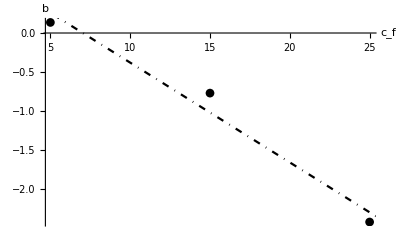

Lambda0B.eps

FittedModel[4424.1+76.9028 x]

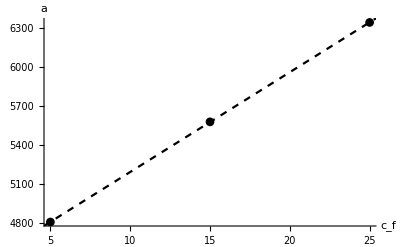

Lambda0A.eps

FittedModel[4371.63+84.5876 x]

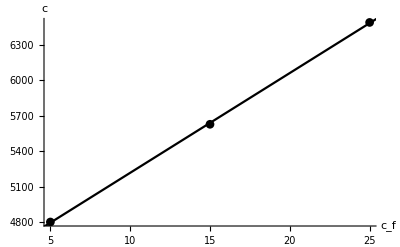

Lambda0C.eps

```mathematica
Bλ0={B/.λ05Fit[[1]][[2]],B/.λ015Fit[[1]][[2]],B/.λ025Fit[[1]][[2]]};
Bλ0Plot = Transpose@{TauxList,Bλ0};
Bλ0Fit= NonlinearModelFit[Bλ0Plot,0*A x^2+B x+CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{Bλ0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["b",FontFamily->"Times New Roman",18]}];
P2 = Plot[{Bλ0Fit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Lambda0B.eps",PlotExport]

Aλ0={Last[λ0Plot5][[2]],Last[λ0Plot15][[2]],Last[λ0Plot25][[2]]};
Aλ0Plot = Transpose@{TauxList,Aλ0};
Aλ0Fit= NonlinearModelFit[Aλ0Plot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{Aλ0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["a",FontFamily->"Times New Roman",18]}];
P2 = Plot[{Aλ0Fit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Lambda0A.eps",PlotExport]

CCλ0={CC/.λ05Fit[[1]][[2]],CC/.λ015Fit[[1]][[2]],CC/.λ025Fit[[1]][[2]]};
CCλ0Plot = Transpose@{TauxList,CCλ0};
CCλ0Fit= NonlinearModelFit[CCλ0Plot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCλ0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["c",FontFamily->"Times New Roman",18]}];
P2 = Plot[{CCλ0Fit[x]},{x,2,60},PlotStyle->{Black},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Lambda0C.eps",PlotExport]
```

FittedModel[0.]

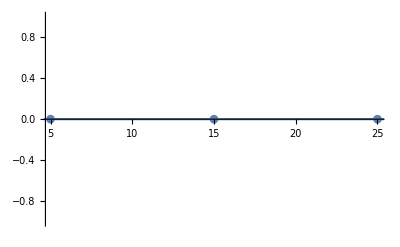

```mathematica
Aλ0={DD/.λ05Fit[[1]][[2]],DD/.λ015Fit[[1]][[2]],DD/.λ025Fit[[1]][[2]]};
Aa0Plot = Transpose@{TauxList,Aλ0};
Aλ0Fit= NonlinearModelFit[Aa0Plot,A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{Aa0Plot},PlotMarkers->Automatic];
P2 = Plot[{Aλ0Fit[x]},{x,2,60}];
Show[P1,P2]
```

FittedModel[4371.63+84.5876 x]

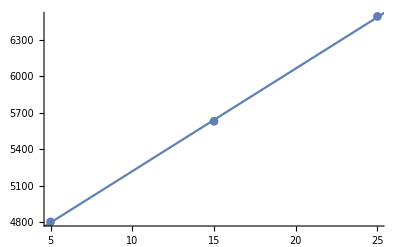

```mathematica
Cλ0={CC/.λ05Fit[[1]][[2]],CC/.λ015Fit[[1]][[2]],CC/.λ025Fit[[1]][[2]]};
Ca0Plot = Transpose@{TauxList,Cλ0};
CCλ0Fit= NonlinearModelFit[Ca0Plot,0*A x^2+B x+CC ,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{Ca0Plot},PlotMarkers->Automatic];
P2 = Plot[{CCλ0Fit[x]},{x,2,60}];
Show[P1,P2]
```

```mathematica
Metaλ0Value[Taux_,NVal_]:=Aλ0Fit[Taux]*NVal^2+Bλ0Fit[Taux] * NVal+CCλ0Fit[Taux]
```

```mathematica
Metaλ0Value[10,6]
```

5215.23

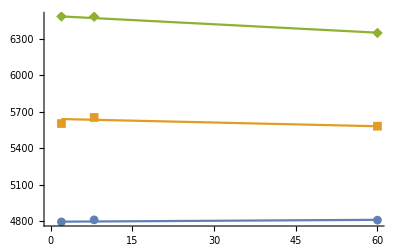

```mathematica
P1=ListPlot[{λ0Plot5,λ0Plot15,λ0Plot25},PlotMarkers->Automatic];
P2 = Plot[{Metaλ0Value[5,x],Metaλ0Value[15,x],Metaλ0Value[25,x]},{x,2,60}];
Show[P1,P2]
```

```mathematica
δ0
```

```mathematica
δ0Data={Matrix2[[5]],Matrix8[[5]],Matrix60[[5]]};
δ0Data//MatrixForm
δ0Data5 = Transpose[δ0Data][[1]];
δ0Data15 = Transpose[δ0Data][[2]];
δ0Data25 = Transpose[δ0Data][[3]];
NList={2,8,60};
TauxList = {5,15,25};
```

(305.322 | 428.41 | 742.941
288.822 | 392.941 | 563.318
284.418 | 365.765 | 522.89)

```mathematica
δ0Plot5 = Transpose@{NList,δ0Data5};
δ0Plot15 = Transpose@{NList,δ0Data15};
δ0Plot25 = Transpose@{NList,δ0Data25};
δ05Fit= NonlinearModelFit[δ0Plot5,Last[δ0Plot5][[2]](1+ Exp[-B x+CC]),{B,CC},x,MaxIterations->1000];
δ015Fit= NonlinearModelFit[δ0Plot15,Last[δ0Plot15][[2]](1+ Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
δ025Fit= NonlinearModelFit[δ0Plot25,Last[δ0Plot25][[2]](1+Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
P1=ListPlot[{δ0Plot5,δ0Plot15,δ0Plot25},PlotMarkers->{Automatic,15},PlotStyle->Black,AxesStyle->Directive[ Black, 24,FontFamily-> "Times New Roman"],ImageSize->{600},PlotLegends->{Style["Data points 5%",FontFamily->"Times New roman",18],Style["Data points 15%",FontFamily->"Times New roman",18],Style["Data points 25%",FontFamily-> "Times New Roman",18]},AxesLabel->{Style["N Value",FontFamily->"Times New Roman"],Style["Moduli (MPa)",FontFamily->"Times New roman"]}];
P2 = Plot[{δ05Fit[x],δ015Fit[x],δ025Fit[x]},{x,2,60},PlotLegends->{Style["5%",FontFamily->"Times New roman",18],Style["15%",FontFamily->"Times New roman",18],Style["25%",FontFamily-> "Times New Roman",18]},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 24]];
```

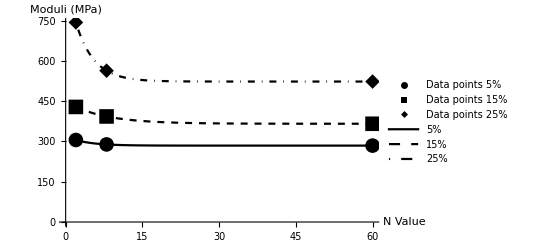

```mathematica
PlotExport=Show[P1,P2]
```

```mathematica
Export["Delta0plot.eps",PlotExport]
```

Delta0plot.eps

FittedModel[0.209941+0.00114074 x]

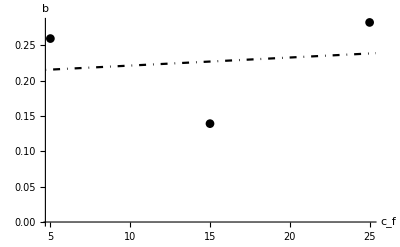

Delta0B.eps

FittedModel[212.171+11.9236 x]

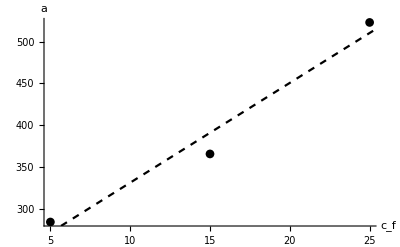

Delta0A.eps

FittedModel[-2.63573+0.0895323 x]

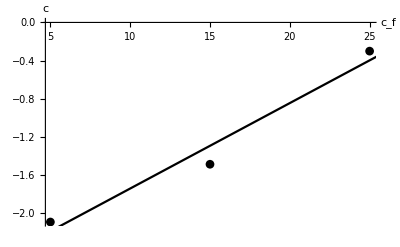

Delta0C.eps

```mathematica
Bδ0={B/.δ05Fit[[1]][[2]],B/.δ015Fit[[1]][[2]],B/.δ025Fit[[1]][[2]]};
Bδ0Plot = Transpose@{TauxList,Bδ0};
Bδ0Fit= NonlinearModelFit[Bδ0Plot,0*A x^2+B x+CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{Bδ0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["b",FontFamily->"Times New Roman",18]}];
P2 = Plot[{Bδ0Fit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Delta0B.eps",PlotExport]

Aδ0={Last[δ0Plot5][[2]],Last[δ0Plot15][[2]],Last[δ0Plot25][[2]]};
Aδ0Plot = Transpose@{TauxList,Aδ0};
Aδ0Fit= NonlinearModelFit[Aδ0Plot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{Aδ0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["a",FontFamily->"Times New Roman",18]}];
P2 = Plot[{Aδ0Fit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Delta0A.eps",PlotExport]

CCδ0={CC/.δ05Fit[[1]][[2]],CC/.δ015Fit[[1]][[2]],CC/.δ025Fit[[1]][[2]]};
CCδ0Plot = Transpose@{TauxList,CCδ0};
CCδ0Fit= NonlinearModelFit[CCδ0Plot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCδ0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["c",FontFamily->"Times New Roman",18]}];
P2 = Plot[{CCδ0Fit[x]},{x,2,60},PlotStyle->{Black},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Delta0C.eps",PlotExport]
```

FittedModel[212.171+11.9236 x]

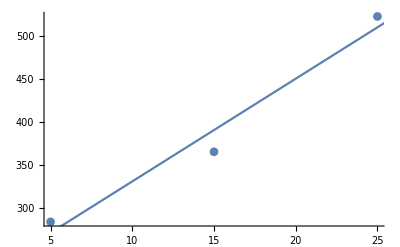

```mathematica
Aδ0={Last[δ0Plot5][[2]],Last[δ0Plot15][[2]],Last[δ0Plot25][[2]]};
Aa0Plot = Transpose@{TauxList,Aδ0};
Aδ0Fit= NonlinearModelFit[Aa0Plot,A x+B,{A,B},x,MaxIterations->500]
P1=ListPlot[{Aa0Plot},PlotMarkers->Automatic];
P2 = Plot[{Aδ0Fit[x]},{x,2,60}];
Show[P1,P2]
```

FittedModel[-2.63573+0.0895323 x]

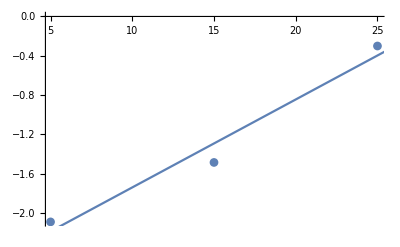

```mathematica
CCδ0={CC/.δ05Fit[[1]][[2]],CC/.δ015Fit[[1]][[2]],CC/.δ025Fit[[1]][[2]]};
CCa0Plot = Transpose@{TauxList,CCδ0};
CCδ0Fit= NonlinearModelFit[CCa0Plot,A x+B,{A,B},x,MaxIterations->500]
P1=ListPlot[{CCa0Plot},PlotMarkers->Automatic];
P2 = Plot[{CCδ0Fit[x]},{x,2,60}];
Show[P1,P2]
```

```mathematica
Metaδ0Value[Taux_,NVal_]:=Aδ0Fit[Taux](1+ Exp[-Bδ0Fit[Taux] NVal+CCδ0Fit[Taux]])
```

```mathematica
Metaδ0Value[15,8]
```

408.479

γ0

(333.153 | 571.659 | 1013.2
329.241 | 524.847 | 775.015
298.203 | 422.526 | 529.608)

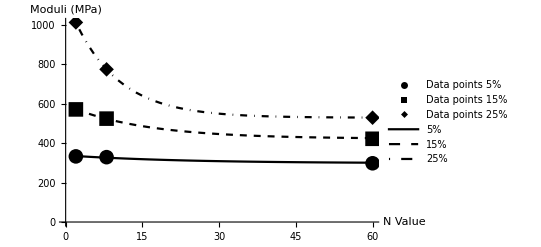

```mathematica
γ0
γ0Data={Matrix2[[6]],Matrix8[[6]],Matrix60[[6]]};
γ0Data//MatrixForm
γ0Data5 = Transpose[γ0Data][[1]];
γ0Data15 = Transpose[γ0Data][[2]];
γ0Data25 = Transpose[γ0Data][[3]];
NList={2,8,60};
TauxList = {5,15,25};

γ0Plot5 = Transpose@{NList,γ0Data5};
γ0Plot15 = Transpose@{NList,γ0Data15};
γ0Plot25 = Transpose@{NList,γ0Data25};
γ05Fit= NonlinearModelFit[γ0Plot5,Last[γ0Plot5][[2]](1+ Exp[-B x+CC]),{B,CC},x,MaxIterations->1000];
γ015Fit= NonlinearModelFit[γ0Plot15,Last[γ0Plot15][[2]](1+ Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
γ025Fit= NonlinearModelFit[γ0Plot25,Last[γ0Plot25][[2]](1+Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
P1=ListPlot[{γ0Plot5,γ0Plot15,γ0Plot25},PlotMarkers->{Automatic,15},PlotStyle->Black,AxesStyle->Directive[ Black, 24,FontFamily-> "Times New Roman"],ImageSize->{600},PlotLegends->{Style["Data points 5%",FontFamily->"Times New roman",18],Style["Data points 15%",FontFamily->"Times New roman",18],Style["Data points 25%",FontFamily-> "Times New Roman",18]},AxesLabel->{Style["N Value",FontFamily->"Times New Roman"],Style["Moduli (MPa)",FontFamily->"Times New roman"]}];
P2 = Plot[{γ05Fit[x],γ015Fit[x],γ025Fit[x]},{x,2,60},PlotLegends->{Style["5%",FontFamily->"Times New roman",18],Style["15%",FontFamily->"Times New roman",18],Style["25%",FontFamily-> "Times New Roman",18]},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 24]];
PlotExport=Show[P1,P2]
```

```mathematica
Export["Gamma0plot.eps",PlotExport]
```

Gamma0plot.eps

```mathematica
γ0
```

γ0

FittedModel[0.0225117+0.00344504 x]

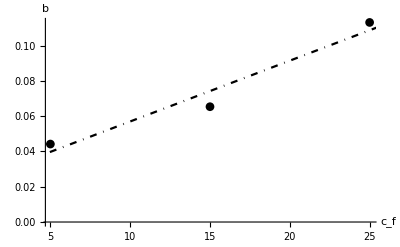

Gamma0B.eps

FittedModel[243.226+11.5702 x]

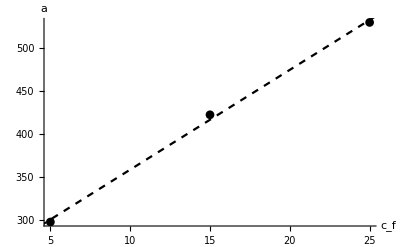

Gamma0A.eps

FittedModel[-2.52788+0.10689 x]

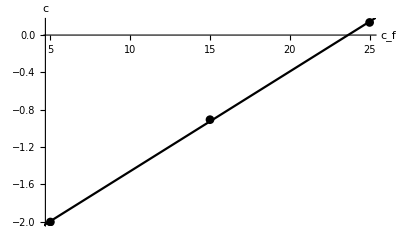

Gamma0C.eps

```mathematica
Bγ0={B/.γ05Fit[[1]][[2]],B/.γ015Fit[[1]][[2]],B/.γ025Fit[[1]][[2]]};
Bγ0Plot = Transpose@{TauxList,Bγ0};
Bγ0Fit= NonlinearModelFit[Bγ0Plot,0*A x^2+B x+CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{Bγ0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["b",FontFamily->"Times New Roman",18]}];
P2 = Plot[{Bγ0Fit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Gamma0B.eps",PlotExport]

Aγ0={Last[γ0Plot5][[2]],Last[γ0Plot15][[2]],Last[γ0Plot25][[2]]};
Aγ0Plot = Transpose@{TauxList,Aγ0};
Aγ0Fit= NonlinearModelFit[Aγ0Plot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{Aγ0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["a",FontFamily->"Times New Roman",18]}];
P2 = Plot[{Aγ0Fit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Gamma0A.eps",PlotExport]

CCγ0={CC/.γ05Fit[[1]][[2]],CC/.γ015Fit[[1]][[2]],CC/.γ025Fit[[1]][[2]]};
CCγ0Plot = Transpose@{TauxList,CCγ0};
CCγ0Fit= NonlinearModelFit[CCγ0Plot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCγ0Plot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["c",FontFamily->"Times New Roman",18]}];
P2 = Plot[{CCγ0Fit[x]},{x,2,60},PlotStyle->{Black},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["Gamma0C.eps",PlotExport]
```

FittedModel[243.226+11.5702 x]

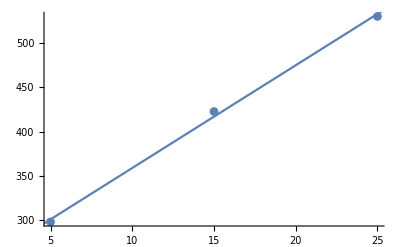

```mathematica
Aγ0={Last[γ0Plot5][[2]],Last[γ0Plot15][[2]],Last[γ0Plot25][[2]]};
Aa0Plot = Transpose@{TauxList,Aγ0};
Aγ0Fit= NonlinearModelFit[Aa0Plot,A x+B,{A,B},x,MaxIterations->500]
P1=ListPlot[{Aa0Plot},PlotMarkers->Automatic];
P2 = Plot[{Aγ0Fit[x]},{x,2,60}];
Show[P1,P2]
```

FittedModel[-2.52788+0.10689 x]

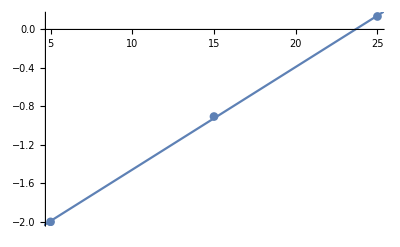

```mathematica
CCγ0={CC/.γ05Fit[[1]][[2]],CC/.γ015Fit[[1]][[2]],CC/.γ025Fit[[1]][[2]]};
CCa0Plot = Transpose@{TauxList,CCγ0};
CCγ0Fit= NonlinearModelFit[CCa0Plot,CC x+B,{CC,B},x,MaxIterations->500]
P1=ListPlot[{CCa0Plot},PlotMarkers->Automatic];
P2 = Plot[{CCγ0Fit[x]},{x,2,60}];
Show[P1,P2]
```

```mathematica
Metaγ0Value[Taux_,NVal_]:=Aγ0Fit[Taux](1+ Exp[-Bγ0Fit[Taux] NVal+CCγ0Fit[Taux]])
Metaγ0Value[5,8]
```

330.922

αL

(1923.06 | 2763.97 | 3643.22
2133.25 | 3378.89 | 4799.98
2320.31 | 3932.86 | 5553.94)

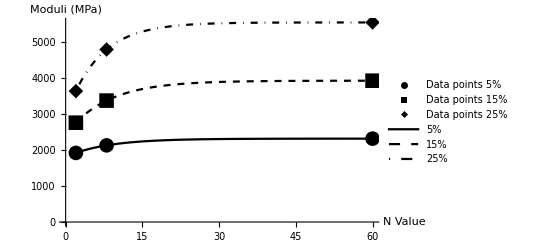

```mathematica
αL
αLData={Matrix2[[7]],Matrix8[[7]],Matrix60[[7]]};
αLData//MatrixForm
αLData5 = Transpose[αLData][[1]];
αLData15 = Transpose[αLData][[2]];
αLData25 = Transpose[αLData][[3]];
NList={2,8,60};
TauxList = {5,15,25};

αLPlot5 = Transpose@{NList,αLData5};
αLPlot15 = Transpose@{NList,αLData15};
αLPlot25 = Transpose@{NList,αLData25};
αL5Fit= NonlinearModelFit[αLPlot5,Last[αLPlot5][[2]](1- Exp[-B x+CC]),{A,B,CC},x,MaxIterations->1000];
αL15Fit= NonlinearModelFit[αLPlot15,Last[αLPlot15][[2]](1- Exp[-B x+CC]),{A,B,CC},x,MaxIterations->1000];
αL25Fit= NonlinearModelFit[αLPlot25,Last[αLPlot25][[2]](1- Exp[-B x+CC]),{A,B,CC},x,MaxIterations->1000];
P1=ListPlot[{αLPlot5,αLPlot15,αLPlot25},PlotMarkers->{Automatic,15},PlotStyle->Black,AxesStyle->Directive[ Black, 24,FontFamily-> "Times New Roman"],ImageSize->{600},PlotLegends->{Style["Data points 5%",FontFamily->"Times New roman",18],Style["Data points 15%",FontFamily->"Times New roman",18],Style["Data points 25%",FontFamily-> "Times New Roman",18]},AxesLabel->{Style["N Value",FontFamily->"Times New Roman"],Style["Moduli (MPa)",FontFamily->"Times New roman"]}];
P2 = Plot[{αL5Fit[x],αL15Fit[x],αL25Fit[x]},{x,2,60},PlotLegends->{Style["5%",FontFamily->"Times New roman",18],Style["15%",FontFamily->"Times New roman",18],Style["25%",FontFamily-> "Times New Roman",18]},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 24]];
PlotExport=Show[P1,P2]
```

```mathematica
Export["AlphaLplot.eps",PlotExport]
```

AlphaLplot.eps

FittedModel[0.112896+0.00147278 x]

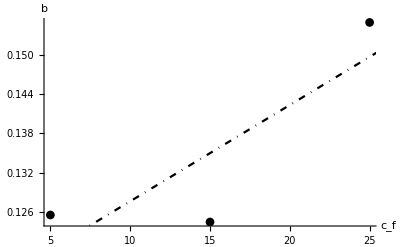

AlphaLB.eps

FittedModel[1510.48+161.682 x]

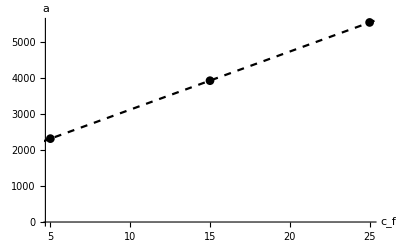

AlphaLA.eps

FittedModel[-1.64601+0.0378386 x]

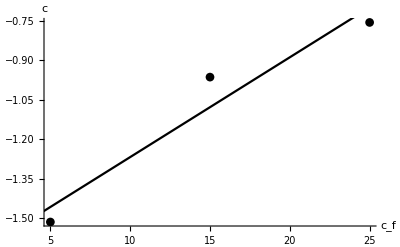

AlphaLC.eps

```mathematica
BαL={B/.αL5Fit[[1]][[2]],B/.αL15Fit[[1]][[2]],B/.αL25Fit[[1]][[2]]};
BαLPlot = Transpose@{TauxList,BαL};
BαLFit= NonlinearModelFit[BαLPlot,0*A x^2+B x+CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{BαLPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["b",FontFamily->"Times New Roman",18]}];
P2 = Plot[{BαLFit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["AlphaLB.eps",PlotExport]

AαL={Last[αLPlot5][[2]],Last[αLPlot15][[2]],Last[αLPlot25][[2]]};
AαLPlot = Transpose@{TauxList,AαL};
AαLFit= NonlinearModelFit[AαLPlot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{AαLPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["a",FontFamily->"Times New Roman",18]}];
P2 = Plot[{AαLFit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["AlphaLA.eps",PlotExport]

CCαL={CC/.αL5Fit[[1]][[2]],CC/.αL15Fit[[1]][[2]],CC/.αL25Fit[[1]][[2]]};
CCαLPlot = Transpose@{TauxList,CCαL};
CCαLFit= NonlinearModelFit[CCαLPlot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCαLPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["c",FontFamily->"Times New Roman",18]}];
P2 = Plot[{CCαLFit[x]},{x,2,60},PlotStyle->{Black},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["AlphaLC.eps",PlotExport]
```

FittedModel[-1.64601+0.0378386 x]

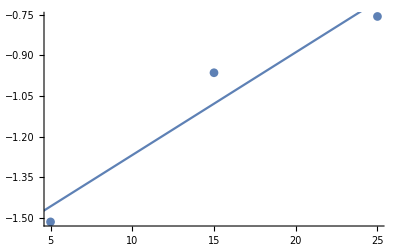

```mathematica
CCαL={CC/.αL5Fit[[1]][[2]],CC/.αL15Fit[[1]][[2]],CC/.αL25Fit[[1]][[2]]};
CCaLPlot = Transpose@{TauxList,CCαL};
CCαLFit= NonlinearModelFit[CCaLPlot,A x+B,{A,B},x,MaxIterations->500]
P1=ListPlot[{CCaLPlot},PlotMarkers->Automatic];
P2 = Plot[{CCαLFit[x]},{x,2,60}];
Show[P1,P2]
```

FittedModel[1510.48+161.682 x]

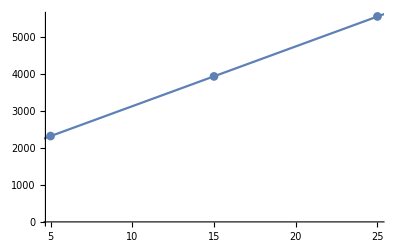

```mathematica
AαL={Last[αLPlot5][[2]],Last[αLPlot15][[2]],Last[αLPlot25][[2]]};
Aa0Plot = Transpose@{TauxList,AαL};
AαLFit= NonlinearModelFit[Aa0Plot,A x+B,{A,B},x,MaxIterations->500]
P1=ListPlot[{Aa0Plot},PlotMarkers->Automatic];
P2 = Plot[{AαLFit[x]},{x,2,60}];
Show[P1,P2]
```

```mathematica
MetaαLValue[Taux_,NVal_]:=AαLFit[Taux](1- Exp[-BαLFit[Taux] NVal+CCαLFit[Taux]])
MetaαLValue[25,2]
```

3508.79

```mathematica
δL
δLData={Matrix2[[8]],Matrix8[[8]],Matrix60[[8]]};
δLData//MatrixForm
δLData5 = Transpose[δLData][[1]];
δLData15 = Transpose[δLData][[2]];
δLData25 = Transpose[δLData][[3]];
NList={2,8,60};
TauxList = {5,15,25};

δLPlot5 = Transpose@{NList,δLData5};
δLPlot15 = Transpose@{NList,δLData15};
δLPlot25 = Transpose@{NList,δLData25};
δL5Fit= NonlinearModelFit[δLPlot5,Last[δLPlot5][[2]](1+ Exp[-B x+CC]),{B,CC},x,MaxIterations->1000];
δL15Fit= NonlinearModelFit[δLPlot15,Last[δLPlot15][[2]](1+ Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
δL25Fit= NonlinearModelFit[δLPlot25,Last[δLPlot25][[2]](1+Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
```

δL

(1788.98 | 2217.7 | 2822.72
1743. | 2127.93 | 2590.71
1728.56 | 2071.1 | 2571.26)

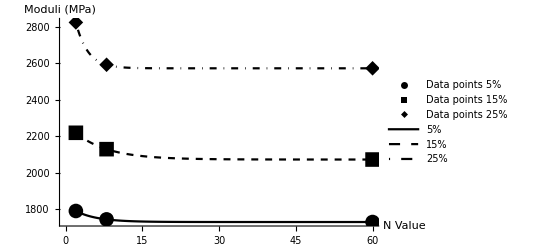

```mathematica
P1=ListPlot[{δLPlot5,δLPlot15,δLPlot25},PlotMarkers->{Automatic,15},PlotStyle->Black,AxesStyle->Directive[ Black, 24,FontFamily-> "Times New Roman"],ImageSize->{600},PlotLegends->{Style["Data points 5%",FontFamily->"Times New roman",18],Style["Data points 15%",FontFamily->"Times New roman",18],Style["Data points 25%",FontFamily-> "Times New Roman",18]},AxesLabel->{Style["N Value",FontFamily->"Times New Roman"],Style["Moduli (MPa)",FontFamily->"Times New roman"]}];
P2 = Plot[{δL5Fit[x],δL15Fit[x],δL25Fit[x]},{x,2,60},PlotLegends->{Style["5%",FontFamily->"Times New roman",18],Style["15%",FontFamily->"Times New roman",18],Style["25%",FontFamily-> "Times New Roman",18]},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 24]];
PlotExport=Show[P1,P2]
```

```mathematica
Export["DeltaLplot.eps",PlotExport]
```

DeltaLplot.eps

FittedModel[0.133312+0.00940188 x]

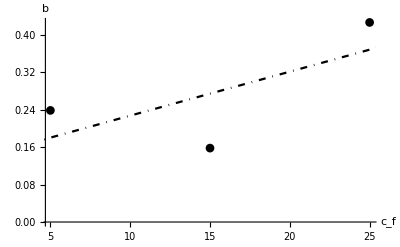

DeltaLB.eps

FittedModel[1491.61+42.1352 x]

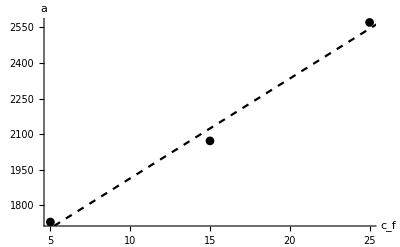

DeltaLA.eps

FittedModel[-3.28049+0.0702422 x]

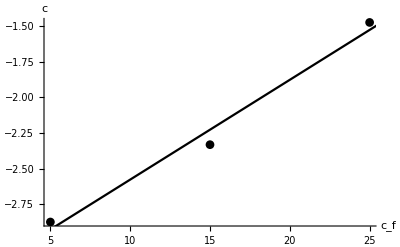

DeltaLC.eps

```mathematica
BδL={B/.δL5Fit[[1]][[2]],B/.δL15Fit[[1]][[2]],B/.δL25Fit[[1]][[2]]};
BδLPlot = Transpose@{TauxList,BδL};
BδLFit= NonlinearModelFit[BδLPlot,0*A x^2+B x+CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{BδLPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["b",FontFamily->"Times New Roman",18]}];
P2 = Plot[{BδLFit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["DeltaLB.eps",PlotExport]

AδL={Last[δLPlot5][[2]],Last[δLPlot15][[2]],Last[δLPlot25][[2]]};
AδLPlot = Transpose@{TauxList,AδL};
AδLFit= NonlinearModelFit[AδLPlot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{AδLPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["a",FontFamily->"Times New Roman",18]}];
P2 = Plot[{AδLFit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["DeltaLA.eps",PlotExport]

CCδL={CC/.δL5Fit[[1]][[2]],CC/.δL15Fit[[1]][[2]],CC/.δL25Fit[[1]][[2]]};
CCδLPlot = Transpose@{TauxList,CCδL};
CCδLFit= NonlinearModelFit[CCδLPlot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCδLPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["c",FontFamily->"Times New Roman",18]}];
P2 = Plot[{CCδLFit[x]},{x,2,60},PlotStyle->{Black},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["DeltaLC.eps",PlotExport]
```

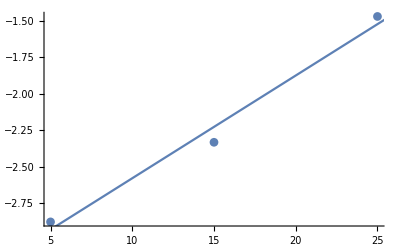

```mathematica
CCδL={CC/.δL5Fit[[1]][[2]],CC/.δL15Fit[[1]][[2]],CC/.δL25Fit[[1]][[2]]};
CCa0Plot = Transpose@{TauxList,CCδL};
CCδLFit= NonlinearModelFit[CCa0Plot,A x+B,{A,B},x,MaxIterations->500];
P1=ListPlot[{CCa0Plot},PlotMarkers->Automatic];
P2 = Plot[{CCδLFit[x]},{x,2,60}];
Show[P1,P2]
```

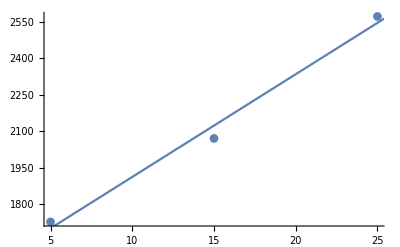

```mathematica
AδL={Last[δLPlot5][[2]],Last[δLPlot15][[2]],Last[δLPlot25][[2]]};
Aa0Plot = Transpose@{TauxList,AδL};
AδLFit= NonlinearModelFit[Aa0Plot,A x+B,{A,B},x,MaxIterations->500];
P1=ListPlot[{Aa0Plot},PlotMarkers->Automatic];
P2 = Plot[{AδLFit[x]},{x,2,60}];
Show[P1,P2]
```

```mathematica
MetaδLValue[Taux_,NVal_]:=AδLFit[Taux](1+ Exp[-BδLFit[Taux] NVal+CCδLFit[Taux]])
MetaδLValue[25,2]
```

2810.26

γL

(1882.13 | 2470.47 | 3137.93
1883.27 | 2410.78 | 3007.51
1801.69 | 2274.21 | 2768.5)

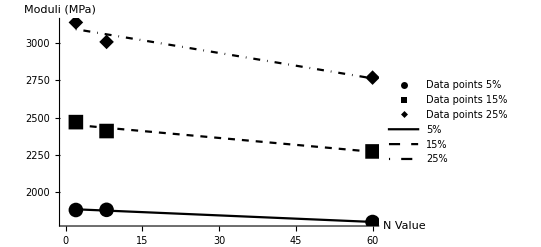

Null

GammaLplot.eps

```mathematica
γL
γLData={Matrix2[[9]],Matrix8[[9]],Matrix60[[9]]};
γLData//MatrixForm
γLData5 = Transpose[γLData][[1]];
γLData15 = Transpose[γLData][[2]];
γLData25 = Transpose[γLData][[3]];
NList={2,8,60};
TauxList = {5,15,25};

γLPlot5 = Transpose@{NList,γLData5};
γLPlot15 = Transpose@{NList,γLData15};
γLPlot25 = Transpose@{NList,γLData25};
γL5Fit= NonlinearModelFit[γLPlot5,A+B x,{A,B},x,MaxIterations->1000];
γL15Fit= NonlinearModelFit[γLPlot15,A+B x,{A,B},x,MaxIterations->3000];
γL25Fit= NonlinearModelFit[γLPlot25,A+B x,{A,B},x,MaxIterations->3000];
P1=ListPlot[{γLPlot5,γLPlot15,γLPlot25},PlotMarkers->{Automatic,15},PlotStyle->Black,AxesStyle->Directive[ Black, 24,FontFamily-> "Times New Roman"],ImageSize->{600},PlotLegends->{Style["Data points 5%",FontFamily->"Times New roman",18],Style["Data points 15%",FontFamily->"Times New roman",18],Style["Data points 25%",FontFamily-> "Times New Roman",18]},AxesLabel->{Style["N Value",FontFamily->"Times New Roman"],Style["Moduli (MPa)",FontFamily->"Times New roman"]}];
P2 = Plot[{γL5Fit[x],γL15Fit[x],γL25Fit[x]},{x,2,60},PlotLegends->{Style["5%",FontFamily->"Times New roman",18],Style["15%",FontFamily->"Times New roman",18],Style["25%",FontFamily-> "Times New Roman",18]},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 24]];
PlotExport=Show[P1,P2]

Export["GammaLplot.eps",PlotExport]
```

FittedModel[-0.244418-0.210813 x]

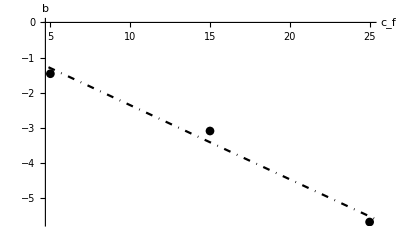

GammaLB.eps

FittedModel[1556.35+48.3409 x]

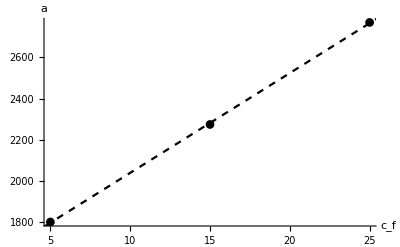

GammaLA.eps

FittedModel[0.+1. CC]

-Graphics-

GammaLC.eps

```mathematica
BγL={B/.γL5Fit[[1]][[2]],B/.γL15Fit[[1]][[2]],B/.γL25Fit[[1]][[2]]};
BγLPlot = Transpose@{TauxList,BγL};
BγLFit= NonlinearModelFit[BγLPlot,0*A x^2+B x+CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{BγLPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["b",FontFamily->"Times New Roman",18]}];
P2 = Plot[{BγLFit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["GammaLB.eps",PlotExport]

AγL={Last[γLPlot5][[2]],Last[γLPlot15][[2]],Last[γLPlot25][[2]]};
AγLPlot = Transpose@{TauxList,AγL};
AγLFit= NonlinearModelFit[AγLPlot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{AγLPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["a",FontFamily->"Times New Roman",18]}];
P2 = Plot[{AγLFit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["GammaLA.eps",PlotExport]

CCγL={CC/.γL5Fit[[1]][[2]],CC/.γL15Fit[[1]][[2]],CC/.γL25Fit[[1]][[2]]};
CCγLPlot = Transpose@{TauxList,CCγL};
CCγLFit= NonlinearModelFit[CCγLPlot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCγLPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["c",FontFamily->"Times New Roman",18]}];
P2 = Plot[{CCγLFit[x]},{x,2,60},PlotStyle->{Black},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["GammaLC.eps",PlotExport]
```

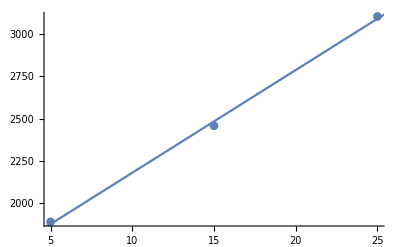

```mathematica
AγL={A/.γL5Fit[[1]][[2]],A/.γL15Fit[[1]][[2]],A/.γL25Fit[[1]][[2]]};
Aa0Plot = Transpose@{TauxList,AγL};
AγLFit= NonlinearModelFit[Aa0Plot,A+B x,{A,B},x,MaxIterations->500];
P1=ListPlot[{Aa0Plot},PlotMarkers->Automatic];
P2 = Plot[{AγLFit[x]},{x,2,60}];
Show[P1,P2]
```

```mathematica
MetaγLValue[Taux_,NVal_]:=AγLFit[Taux]+ BγLFit[Taux] NVal
MetaγLValue[25,2]
```

3079.51

αη

(818.26 | 453.945 | 254.946
590.53 | 236.685 | 102.77
520.105 | 170.375 | 83.6534)

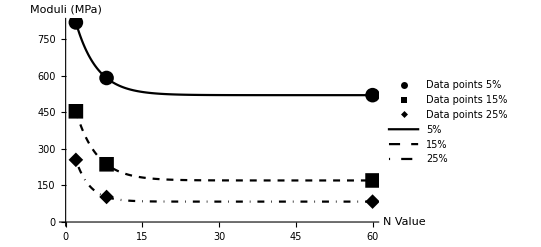

Null

Alphaetaplot.eps

```mathematica
αη
αηData={Matrix2[[10]],Matrix8[[10]],Matrix60[[10]]};
αηData//MatrixForm
αηData5 = Transpose[αηData][[1]];
αηData15 = Transpose[αηData][[2]];
αηData25 = Transpose[αηData][[3]];
NList={2,8,60};
TauxList = {5,15,25};

αηPlot5 = Transpose@{NList,αηData5};
αηPlot15 = Transpose@{NList,αηData15};
αηPlot25 = Transpose@{NList,αηData25};
αη5Fit= NonlinearModelFit[αηPlot5,Last[αηPlot5][[2]](1+ Exp[-B x+CC]),{B,CC},x,MaxIterations->1000];
αη15Fit= NonlinearModelFit[αηPlot15,Last[αηPlot15][[2]](1+ Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
αη25Fit= NonlinearModelFit[αηPlot25,Last[αηPlot25][[2]](1+Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
P1=ListPlot[{αηPlot5,αηPlot15,αηPlot25},PlotMarkers->{Automatic,15},PlotStyle->Black,AxesStyle->Directive[ Black, 24,FontFamily-> "Times New Roman"],ImageSize->{600},PlotLegends->{Style["Data points 5%",FontFamily->"Times New roman",18],Style["Data points 15%",FontFamily->"Times New roman",18],Style["Data points 25%",FontFamily-> "Times New Roman",18]},AxesLabel->{Style["N Value",FontFamily->"Times New Roman"],Style["Moduli (MPa)",FontFamily->"Times New roman"]}];
P2 = Plot[{αη5Fit[x],αη15Fit[x],αη25Fit[x]},{x,2,60},PlotLegends->{Style["5%",FontFamily->"Times New roman",18],Style["15%",FontFamily->"Times New roman",18],Style["25%",FontFamily-> "Times New Roman",18]},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 24]];
PlotExport=Show[P1,P2]

Export["Alphaetaplot.eps",PlotExport]
```

FittedModel[0.285275-0.0119931 x+0.000608034 x^2]

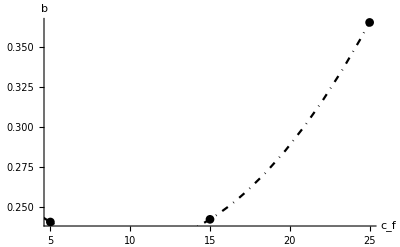

AlphaetaB.eps

FittedModel[793.598-61.2738 x+1.31504 x^2]

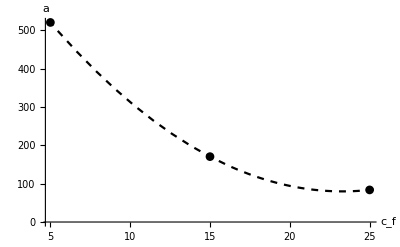

AlphaetaA.eps

FittedModel[-0.840791+0.168464 x-0.0030771 x^2]

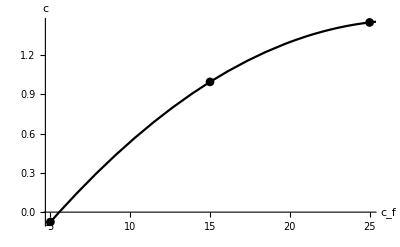

AlphaetaC.eps

```mathematica
Bαη={B/.αη5Fit[[1]][[2]],B/.αη15Fit[[1]][[2]],B/.αη25Fit[[1]][[2]]};
BαηPlot = Transpose@{TauxList,Bαη};
BαηFit= NonlinearModelFit[BαηPlot,A x^2+B x+CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{BαηPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["b",FontFamily->"Times New Roman",18]}];
P2 = Plot[{BαηFit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["AlphaetaB.eps",PlotExport]

Aαη={Last[αηPlot5][[2]],Last[αηPlot15][[2]],Last[αηPlot25][[2]]};
AαηPlot = Transpose@{TauxList,Aαη};
AαηFit= NonlinearModelFit[AαηPlot,A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{AαηPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["a",FontFamily->"Times New Roman",18]}];
P2 = Plot[{AαηFit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["AlphaetaA.eps",PlotExport]

CCαη={CC/.αη5Fit[[1]][[2]],CC/.αη15Fit[[1]][[2]],CC/.αη25Fit[[1]][[2]]};
CCαηPlot = Transpose@{TauxList,CCαη};
CCαηFit= NonlinearModelFit[CCαηPlot,A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCαηPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["c",FontFamily->"Times New Roman",18]}];
P2 = Plot[{CCαηFit[x]},{x,2,60},PlotStyle->{Black},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["AlphaetaC.eps",PlotExport]
```

FittedModel[-0.840791+0.168464 x-0.0030771 x^2]

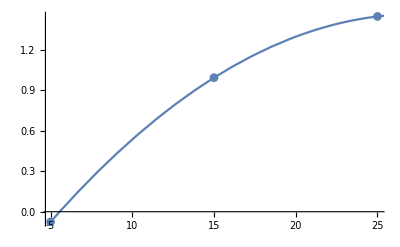

```mathematica
CCαη={CC/.αη5Fit[[1]][[2]],CC/.αη15Fit[[1]][[2]],CC/.αη25Fit[[1]][[2]]};
CCa0Plot = Transpose@{TauxList,CCαη};
CCαηFit= NonlinearModelFit[CCa0Plot,A x^2+B x + CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCa0Plot},PlotMarkers->Automatic];
P2 = Plot[{CCαηFit[x]},{x,2,60}];
Show[P1,P2]
```

FittedModel[793.598-61.2738 x+1.31504 x^2]

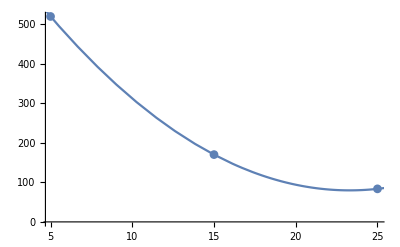

```mathematica
Aαη={Last[αηPlot5][[2]],Last[αηPlot15][[2]],Last[αηPlot25][[2]]};
Aa0Plot = Transpose@{TauxList,Aαη};
AαηFit= NonlinearModelFit[Aa0Plot,A x^2+B x + CC ,{A,B, CC},x,MaxIterations->500]
P1=ListPlot[{Aa0Plot},PlotMarkers->Automatic];
P2 = Plot[{AαηFit[x]},{x,2,60}];
Show[P1,P2]
```

```mathematica
MetaαηValue[Taux_,NVal_]:=AαηFit[Taux](1+ Exp[-BαηFit[Taux] NVal+CCαηFit[Taux]])
MetaαηValue[5,8]
```

590.53

δη

(984.274 | 809.007 | 575.217
1036.71 | 865.733 | 701.583
1049.67 | 912.915 | 717.963)

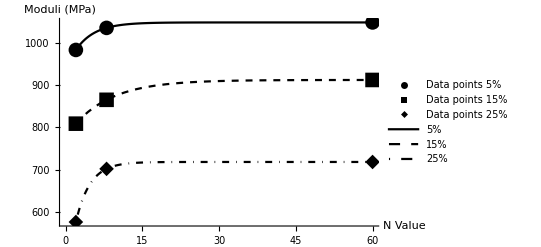

Null

Deltaetaplot.eps

```mathematica
δη
δηData={Matrix2[[11]],Matrix8[[11]],Matrix60[[11]]};
δηData//MatrixForm
δηData5 = Transpose[δηData][[1]];
δηData15 = Transpose[δηData][[2]];
δηData25 = Transpose[δηData][[3]];
NList={2,8,60};
TauxList = {5,15,25};

δηPlot5 = Transpose@{NList,δηData5};
δηPlot15 = Transpose@{NList,δηData15};
δηPlot25 = Transpose@{NList,δηData25};
δη5Fit= NonlinearModelFit[δηPlot5,Last[δηPlot5][[2]](1- Exp[-B x+CC]),{B,CC},x,MaxIterations->1000,Method->"Gradient"];
δη15Fit= NonlinearModelFit[δηPlot15,Last[δηPlot15][[2]](1-Exp[-B x+CC]),{B,CC},x,MaxIterations->3000,Method->"Newton"];
δη25Fit= NonlinearModelFit[δηPlot25,Last[δηPlot25][[2]](1-Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
P1=ListPlot[{δηPlot5,δηPlot15,δηPlot25},PlotMarkers->{Automatic,15},PlotStyle->Black,AxesStyle->Directive[ Black, 24,FontFamily-> "Times New Roman"],ImageSize->{600},PlotLegends->{Style["Data points 5%",FontFamily->"Times New roman",18],Style["Data points 15%",FontFamily->"Times New roman",18],Style["Data points 25%",FontFamily-> "Times New Roman",18]},AxesLabel->{Style["N Value",FontFamily->"Times New Roman"],Style["Moduli (MPa)",FontFamily->"Times New roman"]}];
P2 = Plot[{δη5Fit[x],δη15Fit[x],δη25Fit[x]},{x,2,60},PlotLegends->{Style["5%",FontFamily->"Times New roman",18],Style["15%",FontFamily->"Times New roman",18],Style["25%",FontFamily-> "Times New Roman",18]},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 24]];
PlotExport=Show[P1,P2]

Export["Deltaetaplot.eps",PlotExport]
```

FittedModel[0.185745+0.00455424 x]

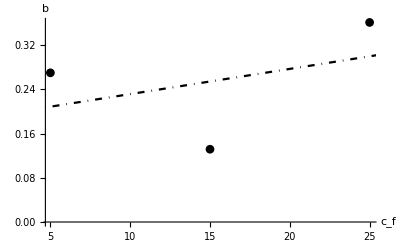

DeltaetaB.eps

FittedModel[1142.3-16.5853 x]

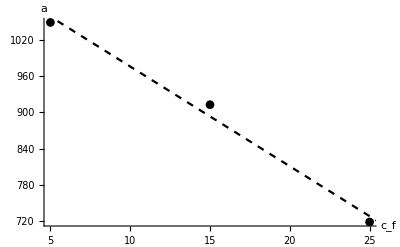

DeltaetaA.eps

FittedModel[-2.68692+0.0671298 x]

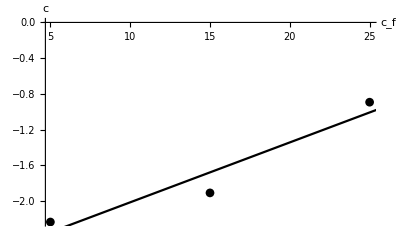

DeltaetaC.eps

```mathematica
Bδη={B/.δη5Fit[[1]][[2]],B/.δη15Fit[[1]][[2]],B/.δη25Fit[[1]][[2]]};
BδηPlot = Transpose@{TauxList,Bδη};
BδηFit= NonlinearModelFit[BδηPlot,0*A x^2+B x+CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{BδηPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["b",FontFamily->"Times New Roman",18]}];
P2 = Plot[{BδηFit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["DeltaetaB.eps",PlotExport]

Aδη={Last[δηPlot5][[2]],Last[δηPlot15][[2]],Last[δηPlot25][[2]]};
AδηPlot = Transpose@{TauxList,Aδη};
AδηFit= NonlinearModelFit[AδηPlot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{AδηPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["a",FontFamily->"Times New Roman",18]}];
P2 = Plot[{AδηFit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["DeltaetaA.eps",PlotExport]

CCδη={CC/.δη5Fit[[1]][[2]],CC/.δη15Fit[[1]][[2]],CC/.δη25Fit[[1]][[2]]};
CCδηPlot = Transpose@{TauxList,CCδη};
CCδηFit= NonlinearModelFit[CCδηPlot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCδηPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["c",FontFamily->"Times New Roman",18]}];
P2 = Plot[{CCδηFit[x]},{x,2,60},PlotStyle->{Black},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["DeltaetaC.eps",PlotExport]
```

FittedModel[-2.68692+0.0671298 x]

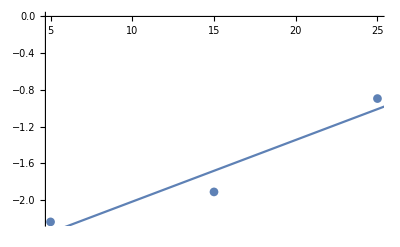

```mathematica
CCδη={CC/.δη5Fit[[1]][[2]],CC/.δη15Fit[[1]][[2]],CC/.δη25Fit[[1]][[2]]};
CCa0Plot = Transpose@{TauxList,CCδη};
CCδηFit= NonlinearModelFit[CCa0Plot,A x+B,{A,B},x,MaxIterations->500]
P1=ListPlot[{CCa0Plot},PlotMarkers->Automatic];
P2 = Plot[{CCδηFit[x]},{x,2,60}];
Show[P1,P2]
```

FittedModel[1142.3-16.5853 x]

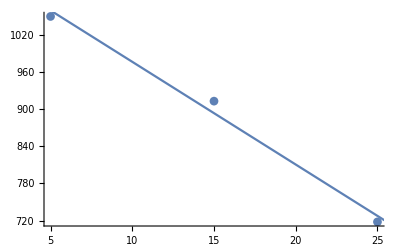

```mathematica
Aδη={Last[δηPlot5][[2]],Last[δηPlot15][[2]],Last[δηPlot25][[2]]};
Aa0Plot = Transpose@{TauxList,Aδη};
AδηFit= NonlinearModelFit[Aa0Plot,A x+B,{A,B},x,MaxIterations->500]
P1=ListPlot[{Aa0Plot},PlotMarkers->Automatic];
P2 = Plot[{AδηFit[x]},{x,2,60}];
Show[P1,P2]
```

```mathematica
MetaδηValue[Taux_,NVal_]:=AδηFit[Taux](1- Exp[-BδηFit[Taux] NVal+CCδηFit[Taux]])
MetaδηValue[25,8]
```

703.511

γη

(1050.45 | 608.545 | 440.776
1152.45 | 684.794 | 595.541
1113.96 | 849.656 | 804.055)

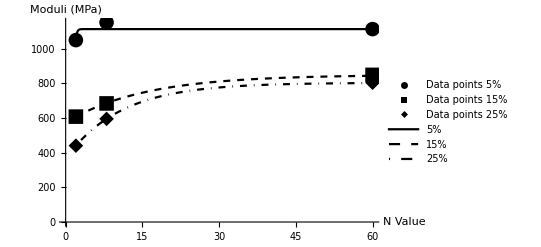

Null

Gammaetaplot.eps

```mathematica
γη
γηData={Matrix2[[12]],Matrix8[[12]],Matrix60[[12]]};
γηData//MatrixForm
γηData5 = Transpose[γηData][[1]];
γηData15 = Transpose[γηData][[2]];
γηData25 = Transpose[γηData][[3]];
NList={2,8,60};
TauxList = {5,15,25};

γηPlot5 = Transpose@{NList,γηData5};
γηPlot15 = Transpose@{NList,γηData15};
γηPlot25 = Transpose@{NList,γηData25};
γη5Fit= NonlinearModelFit[γηPlot5,Last[γηPlot5][[2]](1- Exp[-B x+CC]),{B,CC},x,MaxIterations->1000,Method->"Gradient"];
γη15Fit= NonlinearModelFit[γηPlot15,Last[γηPlot15][[2]](1-Exp[-B x+CC]),{B,CC},x,MaxIterations->3000,Method->"Newton"];
γη25Fit= NonlinearModelFit[γηPlot25,Last[γηPlot25][[2]](1-Exp[-B x+CC]),{B,CC},x,MaxIterations->3000];
P1=ListPlot[{γηPlot5,γηPlot15,γηPlot25},PlotMarkers->{Automatic,15},PlotStyle->Black,AxesStyle->Directive[ Black, 24,FontFamily-> "Times New Roman"],ImageSize->{600},PlotLegends->{Style["Data points 5%",FontFamily->"Times New roman",18],Style["Data points 15%",FontFamily->"Times New roman",18],Style["Data points 25%",FontFamily-> "Times New Roman",18]},AxesLabel->{Style["N Value",FontFamily->"Times New Roman"],Style["Moduli (MPa)",FontFamily->"Times New roman"]}];
P2 = Plot[{γη5Fit[x],γη15Fit[x],γη25Fit[x]},{x,2,60},PlotLegends->{Style["5%",FontFamily->"Times New roman",18],Style["15%",FontFamily->"Times New roman",18],Style["25%",FontFamily-> "Times New Roman",18]},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 24]];
PlotExport=Show[P1,P2]

Export["Gammaetaplot.eps",PlotExport]
```

FittedModel[3.44302 ⅇ^(2.40753-0.421674 x)]

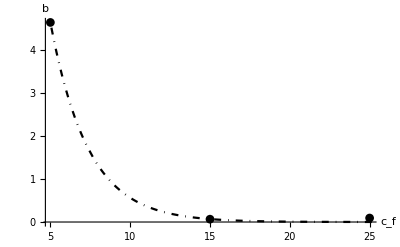

GammaetaB.eps

FittedModel[1154.98-15.4951 x]

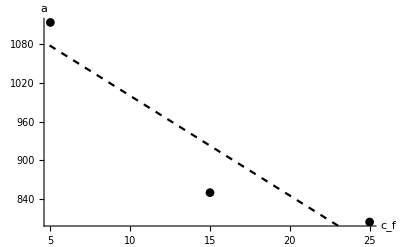

GammaetaA.eps

FittedModel[6.83719-0.35159 x]

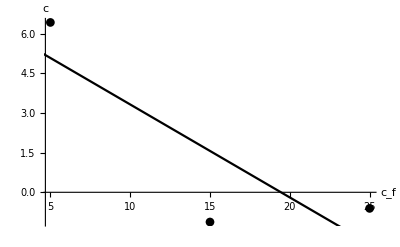

GammaetaC.eps

```mathematica
Bγη={B/.γη5Fit[[1]][[2]],B/.γη15Fit[[1]][[2]],B/.γη25Fit[[1]][[2]]};
BγηPlot = Transpose@{TauxList,Bγη};
BγηFit= NonlinearModelFit[BγηPlot,A Exp[-B x +CC],{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{BγηPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["b",FontFamily->"Times New Roman",18]}];
P2 = Plot[{BγηFit[x]},{x,-20,60},PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["GammaetaB.eps",PlotExport]

Aγη={Last[γηPlot5][[2]],Last[γηPlot15][[2]],Last[γηPlot25][[2]]};
AγηPlot = Transpose@{TauxList,Aγη};
AγηFit= NonlinearModelFit[AγηPlot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{AγηPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["a",FontFamily->"Times New Roman",18]}];
P2 = Plot[{AγηFit[x]},{x,2,60},PlotStyle->{Black,{Black,Dashed}},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["GammaetaA.eps",PlotExport]

CCγη={CC/.γη5Fit[[1]][[2]],CC/.γη15Fit[[1]][[2]],CC/.γη25Fit[[1]][[2]]};
CCγηPlot = Transpose@{TauxList,CCγη};
CCγηFit= NonlinearModelFit[CCγηPlot,0*A x^2+B x +CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCγηPlot},PlotMarkers->Automatic,PlotStyle->{Black,{Black,Dashed},{Black,DotDashed}},AxesStyle->Directive[ Black, 18,FontFamily->"Times New Roman"],ImageSize->{300},AxesLabel->{Style["c_f",FontFamily->"Times New Roman",18],Style["c",FontFamily->"Times New Roman",18]}];
P2 = Plot[{CCγηFit[x]},{x,2,60},PlotStyle->{Black},AxesStyle->Directive[ Black, 18]];
PlotExport=Show[P1,P2]
Export["GammaetaC.eps",PlotExport]
```

FittedModel[13.2192-1.56081 x+0.0403072 x^2]

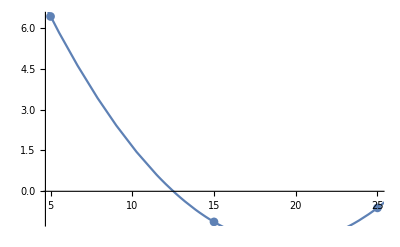

```mathematica
CCγη={CC/.γη5Fit[[1]][[2]],CC/.γη15Fit[[1]][[2]],CC/.γη25Fit[[1]][[2]]};
CCa0Plot = Transpose@{TauxList,CCγη};
CCγηFit= NonlinearModelFit[CCa0Plot,A x^2 +B x + CC,{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{CCa0Plot},PlotMarkers->Automatic];
P2 = Plot[{CCγηFit[x]},{x,2,60}];
Show[P1,P2]
```

FittedModel[9.15023 ⅇ^(4.86524-0.0174932 x)]

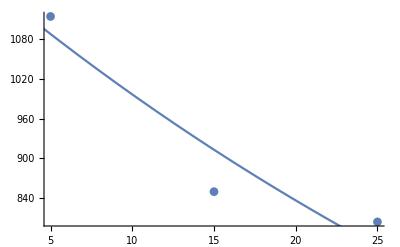

```mathematica
Aγη={Last[γηPlot5][[2]],Last[γηPlot15][[2]],Last[γηPlot25][[2]]};
Aa0Plot = Transpose@{TauxList,Aγη};
AγηFit= NonlinearModelFit[Aa0Plot,A Exp[B x +CC],{A,B,CC},x,MaxIterations->500]
P1=ListPlot[{Aa0Plot},PlotMarkers->Automatic];
P2 = Plot[{AγηFit[x]},{x,2,60}];
Show[P1,P2]
```

```mathematica
MetaγηValue[Taux_,NVal_]:=AγηFit[Taux](1- Exp[-BγηFit[Taux] NVal+CCγηFit[Taux]])
MetaγηValue[5,8]
```

1087.41

```mathematica
MetaModel
```

```mathematica
MetaModel[Taux_,Nval_]:={Metaα0Value[Taux,Nval],Metaβ0Value[Taux,Nval],Metaλ0Value[Taux,Nval],Metaδ0Value[Taux,Nval],Metaγ0Value[Taux,Nval],MetaαLValue[Taux,Nval],MetaδLValue[Taux,Nval],MetaγLValue[Taux,Nval],MetaαηValue[Taux,Nval],MetaδηValue[Taux,Nval],MetaγηValue[Taux,Nval]}
```

```mathematica
MetaγLValue[25,60]
```

2759.66

```mathematica
MetaModel[25,60]
```

{10140.4,8470.91,6348.09,510.26,533.389,5552.17,2544.99,2759.66,83.6534,727.662,374.054}

```mathematica
Save["MetaModel.m",MetaModel]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Import["MetaModel.m"];
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Transpose::nmtx: The first two levels of {{5,15,25},Aγη} cannot be transposed.

NonlinearModelFit::fitd: First argument Transpose[{{5,15,25},Aγη}] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit::nrlnum: The function value {-4.64371+1. 2.71828^(1.+Bx),-0.0657759+1. 2.71828^(1.+Bx),-0.0926641+1. 2.71828^(1.+Bx)} is not a list of real numbers with dimensions {3} at {A,B,CC} = {1.,1.,1.}.

```mathematica
MetaModel[15,4]
```

{5597.05,7965.95,5636.36,434.31,539.667,3155.57,2200.09,2469.92,345.078,833.238,687.265}